## MNIST Classifier2: LeNet

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
```

```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
result=NetTrain[lenetModel,trainingData,All,ValidationSet->testData]
```

NetTrainResultsObject[<>]

```mathematica
trained=result["TrainedNet"]
```

NetChain[<>]

```mathematica
cm=ClassifierMeasurements[trained,testData]
```

ClassifierMeasurementsObject[…]

Obtain the accuracy of the network on the validation set:

```mathematica
cm["Accuracy"]
```

0.9889

Obtain a plot of the confusion matrix of the network on the validation set:

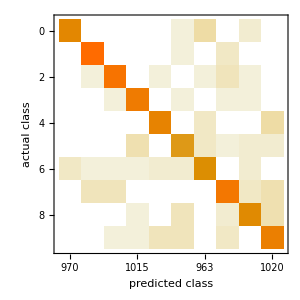

```mathematica
cm["ConfusionMatrixPlot"]
```